Magnetic Potential

```mathematica
a = 1; 
Ic = 100;
```

```mathematica
A[x_,z_]:=Ic a NIntegrate[Exp[-k z]BesselJ[1,k x]BesselJ[1,k a],{k,0,13}]/Pi
```

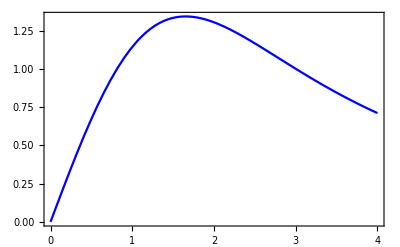

```mathematica
Plot[A[x,2a],{x,0,4},Frame->True, 
PlotStyle->{Blue,Darker}]
```

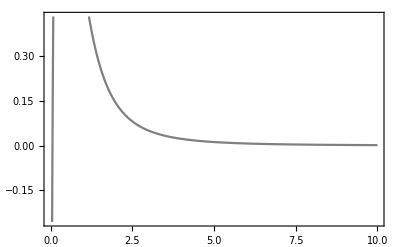

```mathematica
Plot[A[0.1,z],{z,0,10},
Frame->True, 
PlotStyle->Gray]
```

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
Brad[ρ_,z_]:=-ND[A[ρ,x],x,z]
```

```mathematica
Bz[ρ_,z_]:= ND[x A[x,z],x,ρ]/ρ
```

```mathematica
B[ρ_,z_]:={Brad[ρ,z],0,Bz[ρ,z]}
```

Components of magnetic field

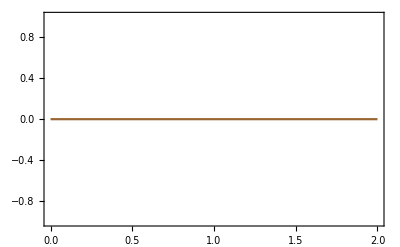

```mathematica
Plot[Brad[x,0.2],{x,0,2a},
Frame->True,
PlotStyle->Brown]
```

```mathematica
Plot[Brad[0.2,x],{x,0,2a},
Frame->True,
PlotStyle->Brown]
```

-Graphics-

```mathematica
Plot[Bz[0.2,x],{x,0,2a},
Frame->True,
PlotStyle->Brown]
```

-Graphics-